```mathematica
BeginPackage["MeFuncs`"];

xH={1,0};
yH={0,1};
rH={Cos[#],Sin[#]}&;

$PrePrint=StandardForm;
(*Begin["`Private`"]*)
CsQ:=DeleteElements[#[[1]]*#[[2]],{0}]&[{#,Flatten[Attributes[#]/.{Constant->1,{}->{0}}]}]&[Vars[#]]&
Flatn:=DeleteElements[#[[2]],#[[1]]]&[Flatten/@{{List@@({##}/.#1->{Null})},#1}]&
FNCheck:=Module[{},Print[{#1,#2,#3}];Print[Defer[#2[#1]==#3[#1]]];#2[#1]==#3[#1]]&
Intg:=Extract[#,Flatn[{Position[#,Integrate]},0]][[1]]&[FullForm[#]]&
Intl:=Extract[#,Flatn[{Position[#,Integrate]},0]][[2]]&[FullForm[#]]&
Mag:=If[VectorQ[#],Sqrt[#.#],#]&;
RP:=If[AnyMatch[{0,Null},#[[1]]],#[[2]],#[[2]]//.Thread[#[[3]]->#[[4]]]]&[{(Times@@Flatten[{##}/.Thread[{#1,#2,#3}->{1,1,1}]]),#1,#2,#3}]&
(*SS:=#1/.Solve[#2==0,#1][[If[#3===Null,1,(Times@@{##}/.Thread[{#1,#2}->{1,1}])]]]&*)
SS:=#[[1]]/.Solve[#[[2]]==0,#[[1]]][[If[#[[3]]===Null,1,#[[3]]]]]&[{#1,#2,Times@@({##}/.Thread[{#1,#2}->{1,1}])}]&
S:=If[#2===3,#1/.g21[],#1]&[If[AnyMatch[{2,3},#2],FactorTerms[#1,CsQ[#1]],#1],#2]&[If[AnyMatch[{0,Null},#2],#1,
Refine[FullSimplify[#1],Variables[#1]∈Reals]/.Abs[q_]:>q],#2]&[#1,(Times@@({##}/.#1->1))]&;
g21:=Express_:>Module[{},
Express/.(Thread[#[[2,3]]*Join[#[[1,2]],#[[2,2]]]->#[[2,3]]*ConstantArray[1,Length[Join[#[[1,2]],#[[2,2]]]]]])&[{{Vars[#[[1]]],DeleteCases[(Boole[MemberQ[Attributes[#],Constant]&/@Vars[#[[1]]]])*(#&/@Vars[#[[1]]]),0]},{#[[1]],#[[2]],#[[3]]}}]&[{Express,#[[1]],#[[2]]}]&[If[Times@@{##}===1,
{{},1},
If[ContainsAny[{0},{##}]||ContainsAny[{Null},{##}],
{{##}[[1]],0},
{{##}[[1]],1}]]]]&
Trm:=If[Head[Expand[#]]===Plus,List@@Expand[#],{#}]&;
Vars:=If[AnyMatch[{0,Null},#[[2]]],(DeleteCases[Dt/@#[[1]],0]/.HoldPattern[Dt[q_]]:>q),#[[1]]]&[{Variables[#[[1]]//.{f_[q_]|Exp[q_]:>q}],#[[2]]}]&[{(If[Head[Trm[#1][[1]]]===Power,(Trm[#1][[1,1]]),Trm[#1]]),(Times@@Flatten[{##}/.#1->1])}]&
(*!FreeQ[#,Integrate]*)
QA:=Table[#1,{#2,#3}]&[#1,If[AnyMatch[{1,Null},#1],i,Vars[#1][[1]]],#2]&;

d:=Nest[Dt,#1,(Times@@{##}/.#1->1)]//.HoldPattern[Dt[q_Symbol]]->Derivative[1][q]&
Format[Derivative[n_][f_]]=OverDot[f,n];

PRM[param_:t,unParam_:0]:=Express_:>Module[{Terms,vars,args,maps},
Catch[
Terms=If[Head[Expand[#]]===Plus,List@@Expand[#],{#}]&[Express/.g21[]];
vars=Variables[Terms];
If[!unParam==0,Throw[Express/.(q_[param]->q&)/@vars]];
args=Vars[vars];
maps=Table[If[!MatchQ[vars[[i]],Derivative[n_][f_][param]|Derivative[n_][f_]],
vars[[i]]/.(#->#[param]&)/@args,
If[MatchQ[vars[[i]],Derivative[n_][f_]],
vars[[i]]/.Derivative[n_][f_]->Derivative[n][f][param],
vars[[i]]
]
],
{i,Length[vars]}];
Express/.Thread[vars->maps]
]
];

(*End[]*)
EndPackage[]
```

```mathematica
Quit
```

```mathematica
ClearAll["Global`*"]
SetAttributes[{m,g},Constant]
$Assumptions=t>=0&&t0>=0&&tf>=0&&m>0&&g>0;
```

```mathematica
SetAttributes[IntTricks,HoldAll];
IntTricks=Integrate[expr_,{t,t0_,tf_}]:>
Module[{Terms,Tricks,DoATrick,Integrals,FnDecoder,InverseSubs,Result},
Terms=If[Head[expr]===Plus,List@@expr,{expr}];

Tricks={(*Order matters here. Terms will go to first match => Complex to simple listing chosen*)
c_.*f1_[t]*f2_[q_[t]]*q_'[t]:>c*f1[t]*Integrate[f2[q],{q,q[t0],q[tf]}],
c_.*f_[c1_*q_[t]]*q_'[t]:>c*Integrate[f[c1*q],{q,q[t0],q[tf]}]/;NumberQ[c1],
c_.*f1_[c1_*q1_[t]]*f2_[c2_*q2_[t]]*q2_'[t]:>c*f1[c1*q1[t]]*Integrate[f2[c2*q2],{q2,q2[t0],q2[tf]}]/;NumberQ[c1]&&NumberQ[c2],
(*c_.*f_.[t]*q_'[t]:>c*((f[tf]*q[tf]-f[t0]*q[t0])-Integrate[q[t]*f'[t],{t,t0,tf}]),(*half trick*)*)
(*c_.*f_.[t]*q_.[t]:>c*((f[tf]*(Integrate[q[t],t]/.t->tf)-f[t0]*(Integrate[q[t],t]/.t->t0))-Integrate[(Integrate[q[t],t])*f'[t],{t,t0,tf}]),(*bad trick*)*)
c_.*q_'[t]:>c*Integrate[1,{q,q[t0],q[tf]}],
c_.*((q_'[t])^2)^(1/2):>c*Integrate[1,{q,q[t0],q[tf]}],
(*c_.*f_.[q_[t]]:>c*((f[q[tf]]*tf-f[q[t]]*t0)-Integrate[t*d[f[q[t]]],{t,t0,tf}]),(*bad trick*)
c_.*(f_.[q_[t]])^2:>c*(((Integrate[f[q[t]],t]/.t->tf)*tf-(Integrate[f[q[t]],t]/.t->t0)*t0)-Integrate[t*d[f[q[t]]],{t,t0,tf}]),(*bad trick*)*)
c_.*f_.[t]:>c*Integrate[f[t],{t,t0,tf}],
(c_.*(f1_.[q_[t]]*q_'[t])^(2)+c_.*(f2_.[q_[t]]*q_'[t])^(2))^(1/2):>c*Integrate[(f1[q]^(2)+f2[q]^(2))^(1/2),{q,q[t0],q[tf]}],
c_.*((f_.[q_[t]]*q_'[t])^(2))^(1/2):>c*Integrate[f[q]^(2),{q,q[t0],q[tf]}]
};(*pattern_:>replacement_/;Inactive[Integrate[pattern,x]]===Integrate[pattern,x]*)

DoATrick[term_]:=Module[{WhichTrick},
	WhichTrick=SelectFirst[Tricks,MatchQ[term,#[[1]]]&];
If[MissingQ[WhichTrick],term,term/. WhichTrick]];

	Integrals=DoATrick/@Terms;
Result=Plus@@Integrals/.{t0->0,tf->t}(*/.InverseSubs*)
];/;FreeQ[expr,Integrate];

V2D[Integrand_]:=-Integrate[Integrand,{t,t0,tf}];

ELeq[T_,V_,qs_,Cons_,ShowBool_:0]:=
Module[{L,λs,ELUnCons,ConsQ,ELCons,EqnsUnCon,EqnsCon,Show},
		L=T-V;

	ELUnCons[Lag_,var_]:=D[D[Lag,D[var,t]],t]-D[Lag,var];
	EqnsUnCon=Table[ELUnCons[L,qs[[i]]],{i,Length[qs]}];
If[Length[Cons]==0,
EqnsCon={};,

	λs=Symbol/@("λ"<>ToString[#]&/@Range[Length[Cons]]);
ELCons[UnkMult_,Constraint_,var_]:=UnkMult*D[Constraint,var];
EqnsCon=Table[ELCons[λs[[i]],Cons[[i]],qs[[j]]],{i,1,Length[Cons]},{j,1,Length[qs]}];
];

Show=If[ShowBool==1,
Print[L];
Print[TableForm[EqnsUnCon-Total[EqnsCon],
TableHeadings->{qs,None},TableSpacing->{1,5}]];
If[Length[Cons]>0,
Print[TableForm[Flatten[EqnsCon],
TableHeadings->{Tuples[{λs,qs}],None},TableSpacing->{1,5}]];
]
];
Return[Join[EqnsUnCon-Total[EqnsCon],EqnsCon]]
]
```

```mathematica
C2P=RP[#,{x,y},{r*Cos[a],r*Sin[a]},1]&; (*Use like C2P@{x,y}*)
P2C=RP[#,{r,Cos[a],Sin[a]},{Sqrt[x^2+y^2],x/Sqrt[x^2+y^2],y/Sqrt[x^2+y^2]}]&;
```

```mathematica
TC[x_,y_]=m/2(d[x]^2+d[y]^2);TC[t_]=TC[x,y]/.PRM[]
TP[r_,a_]=m/2(d[r*Cos[a]]^2+d[r*Sin[a]]^2);TP[t_]=TP[r,a]/.PRM[]

	Ipill[r]=RP[Integrate[(M2/r)r'^2,{r',0,r}],{r,M2},{2*h/3,2/3*M}];
TPpill[a_]=1/2Ipill[r]*d[a]^2
```

1/2 m ((ẋ[t])^2+(ẏ[t])^2)

1/2 m ((-r[t] Sin[a[t]] ȧ[t]+Cos[a[t]] ṙ[t])^2+(Cos[a[t]] r[t] ȧ[t]+Sin[a[t]] ṙ[t])^2)

4/81 h^2 M (ȧ)^2

```mathematica
Fg={0,-m*g};FN[a_]=m*g*Sin[a]*{Cos[a],Sin[a]};F[a_]=Fg+FN[a]
```

{g m Cos[a] Sin[a],-g m+g m Sin[a]^2}

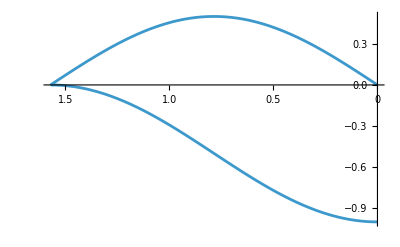

```mathematica
Plot[RP[{#[[1,1]],#[[1,2]]},{m,g},{1,1}],{a,π/2,0},ScalingFunctions->{"Reverse",Identity}]&[{F[a],FN[a]}]
```

```mathematica
lC[x_,y_]:={x,y}; lP[r_,a_]:={r*Cos[a],r*Sin[a]};
dlC[x_,y_]:=d[lC[x,y]];dlP[r_,a_]:=RP[d[lP[r,a]],{r,r'},{R,0},];
dlC[x,y];
dlP[r,a];
Vintgs={S[(P2C/@F[a]).dlC[x,y]],S[(P2C/@F[a]).dlC[x,y]]/.PRM[],S[F[a].dlP[r,a]],S[F[a].dlP[r,a]]/.PRM[]}
VCint[x_,y_]=Vintgs[[1]];VCint[t_]=Vintgs[[2]];
VPint[r_,a_]=Vintgs[[3]];VPint[t_]=Vintgs[[4]];
```

{(g m x (y ẋ-x ẏ))/(x^2+y^2),(g m x[t] (y[t] ẋ[t]-x[t] ẏ[t]))/(x[t]^2+y[t]^2),-g m r Cos[a] ȧ,-g m Cos[a[t]] r[t] ȧ[t]}

```mathematica
RP[VPint[t]/.g21[{r[t]},],{r'[t]},{0},]
S[(Integrate[VPint[t],{t,t0,tf}]/.IntTricks),2]
```

-g m Cos[a[t]] r[t] ȧ[t]

g m (r[t] Sin[a[0]]-r[t] Sin[a[t]])

```mathematica
Vs=RP[{V2D[VCint[x,y]],V2D[VCint[t]],V2D[VPint[r,a]],S[V2D[VPint[t]]/.IntTricks,1]},{t0,tf},{0,t},0]
VC[x_,y_]=Vs[[1]];VC[t_]=Vs[[2]];
VP[r_,a_]=Vs[[3]];VP[t_]=Vs[[4]];
```

{-(g m (-t0+tf) x (y ẋ-x ẏ))/(x^2+y^2),-∫_t0^tf (g m x[t] (y[t] ẋ[t]-x[t] ẏ[t]))/(x[t]^2+y[t]^2)ⅆt,g m r (-t0+tf) Cos[a] ȧ,g m r[t] (-Sin[a[0]]+Sin[a[t]])}

Spacial functions don’t really work / mean anything here. I’d have to chain rule it out with the t integral (which int tricks does to make the time varying integrands equivalent integrate to what their space varying ones would give.)

```mathematica
LC[t_]:=RP[TC[t]-VC[t],{r[t],r'[t]},{R,0},0];LP[t_]:=RP[TP[t]-S[VP[t],2],{r[t],r'[t]},{R,0},0];
LC[x_,y_]:=RP[TC[x,y]-(VC[t]/.PRM[t,1]),{r[t],r'[t]},{R,0},0];LC[x,y];
LP[r_,a_]:=RP[TP[r,a]-(VP[t]/.PRM[t,1]),{r[t],r'[t]},{R,0},0];LP[r,a];
LC[t]
LP[t]
```

∫_t0^tf (g m x[t] (y[t] ẋ[t]-x[t] ẏ[t]))/(x[t]^2+y[t]^2)ⅆt+1/2 m ((ẋ[t])^2+(ẏ[t])^2)

g m (r[t] Sin[a[0]]-r[t] Sin[a[t]])+1/2 m ((-r[t] Sin[a[t]] ȧ[t]+Cos[a[t]] ṙ[t])^2+(Cos[a[t]] r[t] ȧ[t]+Sin[a[t]] ṙ[t])^2)

```mathematica
ParametricPlot[{{Sin[t],Cos[t]},{Sin[t],RP[Fg.lP,{m,g,r,a},{1,9.8,1,t},1]}},{t,π/2,0},AxesLabel->{"x","y"},AspectRatio->1];
```

```mathematica
Conx[t_]:=x[t]^2+y[t]^2-R^2
Cony[t_]:=x[t]^2+y[t]^2-R^2
ELegsC[t_]=ELeq[TC[t],VC[t],{x[t],y[t]},{Conx[t],Cony[t]},1];
```

∫_t0^tf (g m x[t] (y[t] ẋ[t]-x[t] ẏ[t]))/(x[t]^2+y[t]^2)ⅆt+1/2 m ((ẋ[t])^2+(ẏ[t])^2)

x[t] | -∫_t0^tf (-(g m x[t] ẏ[t])/(x[t]^2+y[t]^2)-(2 g m x[t]^2 (y[t] ẋ[t]-x[t] ẏ[t]))/((x[t]^2+y[t]^2)^2)+(g m (y[t] ẋ[t]-x[t] ẏ[t]))/(x[t]^2+y[t]^2))ⅆt-2 λ1 x[t]-2 λ2 x[t]+m ẍ[t]
y[t] | -∫_t0^tf ((g m x[t] ẋ[t])/(x[t]^2+y[t]^2)-(2 g m x[t] y[t] (y[t] ẋ[t]-x[t] ẏ[t]))/((x[t]^2+y[t]^2)^2))ⅆt-2 λ1 y[t]-2 λ2 y[t]+m ÿ[t]

{λ1,x[t]} | 2 λ1 x[t]
{λ1,y[t]} | 2 λ1 y[t]
{λ2,x[t]} | 2 λ2 x[t]
{λ2,y[t]} | 2 λ2 y[t]

```mathematica
Conr[t_]:=r[t]-R
Cona[t_]=S[Mag[Fg*Sin[a[t]]-(FN[a]/.PRM[])]-m*r[t]*a'[t]^2]
ELegsP[t_]=ELeq[S[TP[t]],S[VP[t]],{r[t],a[t]},{Conr[t],Cona[t]},1];
```

√2 g m Sin[a[t]] √(1+Sin[a[t]])-m r[t] (ȧ[t])^2

-g m r[t] (-Sin[a[0]]+Sin[a[t]])+1/2 m (r[t]^2 (ȧ[t])^2+(ṙ[t])^2)

r[t] | -λ1+g m (-Sin[a[0]]+Sin[a[t]])+m λ2 (ȧ[t])^2-m r[t] (ȧ[t])^2+m r̈[t]
a[t] | g m Cos[a[t]] r[t]-λ2 ((g m Cos[a[t]] Sin[a[t]])/(√2 √(1+Sin[a[t]]))+√2 g m Cos[a[t]] √(1+Sin[a[t]]))+2 m r[t] ȧ[t] ṙ[t]+m r[t]^2 ä[t]

{λ1,r[t]} | λ1
{λ1,a[t]} | 0
{λ2,r[t]} | -m λ2 (ȧ[t])^2
{λ2,a[t]} | λ2 ((g m Cos[a[t]] Sin[a[t]])/(√2 √(1+Sin[a[t]]))+√2 g m Cos[a[t]] √(1+Sin[a[t]]))

```mathematica
ErT[t_]=RP[ELeq[S[TP[t]],VP[t],{r[t],a[t]},{Conr[t],Cona[t]}][[1]],{λ1,λ2},{0,0},1];
EaT[t_]=RP[ELeq[S[TP[t]],VP[t],{r[t],a[t]},{Conr[t],Cona[t]}][[2]],{λ1,λ2},{0,0},1];
EPtotT[t_]=S[ErT[t]+EaT[t],0];
```

```mathematica
EPs=RP[{{S[ErT[t]/.PRM[t,1]]},{S[EaT[t]/.PRM[t,1]]},{S[EPtotT[t]/.PRM[t,1]]}},{},{}]
EPs0=RP[EPs,{r',r''},{0,0}]
Er=EPs[[1,1]];Ea=EPs[[2,1]];EPtot=EPs[[3,1]];

EPCs={{#[[3,1]],#[[3,2]]},{#[[4,1]],#[[4,2]]}}&[S[RP[ELeq[TP[t],VP[t],{r[t],a[t]},{Conr[t],Cona[t]}],{λ1,λ2},{0,0},1],1]]/.PRM[t,1]
```

{{m (g (Sin[a]-Sin[a[0]])-r (ȧ)^2+r̈)},{m r (g Cos[a]+2 ȧ ṙ+r ä)},{m (g (r Cos[a]+Sin[a]-Sin[a[0]])+r (-(ȧ)^2+2 ȧ ṙ+r ä)+r̈)}}

{{m (g (Sin[a]-Sin[a[0]])-r (ȧ)^2)},{m r (g Cos[a]+r ä)},{m (g (r Cos[a]+Sin[a]-Sin[a[0]])+r (-(ȧ)^2+r ä))}}

{{0,0},{0,0}}

```mathematica
ErSols={SS[a',Er],SS[r'',Er]}
EaSols={SS[a',Ea],SS[a'',Ea],SS[r',Ea]}
```

{-(√(g Sin[a]-g Sin[a[0]]+r̈))/(√r),-g Sin[a]+g Sin[a[0]]+r (ȧ)^2}

{(-g Cos[a]-r ä)/(2 ṙ),(-g Cos[a]-2 ȧ ṙ)/r,(-g Cos[a]-r ä)/(2 ȧ)}

```mathematica
RP[S[RP[Ea,{a'},{ErSols[[1]]}]],{r',r''},{0,0}]
SS[a'',%]
```

m r (g Cos[a]+r ä)

-(g Cos[a])/r

```mathematica
EPs=RP[RP[{{S[ErT[t]/.PRM[t,1]]},{S[EaT[t]/.PRM[t,1]]},{S[EPtotT[t]/.PRM[t,1]]}},{a''},{-(g/r)*Cos[a]}],{r',r''},{0,0}]
Er=EPs[[1,1]];Ea=EPs[[2,1]];EPtot=EPs[[3,1]];
```

{{m (g (Sin[a]-Sin[a[0]])-r (ȧ)^2)},{0},{m (g (r Cos[a]+Sin[a]-Sin[a[0]])+r (-g Cos[a]-(ȧ)^2))}}

```mathematica
SS[a',Er]
```

-(√g √(Sin[a]-Sin[a[0]]))/(√r)

```mathematica
S[RP[Cona[t]/.PRM[t,1],{a'},{SS[a',Er]}]]
SS[a[0],%]
```

g m (Sin[a] (-1+√2 √(1+Sin[a]))+Sin[a[0]])

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

ArcSin[Sin[a]-√2 Sin[a] √(1+Sin[a])]

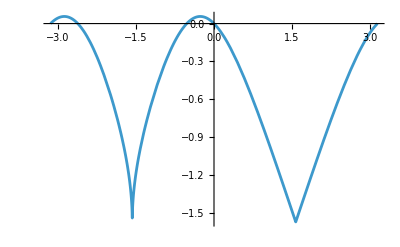

```mathematica
Plot[ArcSin[Sin[a]-√2 Sin[a] √(1+Sin[a])],{a,- π, π}]
```